## SpinTaylorF2 Evolution Code

Initial configuration

```mathematica
Subscript[m, 1]= 12.4;
Subscript[m, 2]= 1.4;
χ = 0.5; 
κ = 0.5;
Subscript[f, 0]= 15;
```

Expressions

```mathematica
Eγ = N[EulerGamma,50];
```

```mathematica
M = Subscript[m, 1] + Subscript[m, 2];
```

```mathematica
Subscript[f, LSO] =6^(-3/2)/(π M)
```

0.00156944

```mathematica
v[f_] := (M π f)^(1/3);
```

```mathematica
Subscript[v, 0] = v[Subscript[f, 0]]
```

8.66377

```mathematica
Subscript[v, LSO] = v[Subscript[f, LSO]]
```

0.408248

```mathematica
η = (Subscript[m, 1] Subscript[m, 2])/(Subscript[m, 1]+ Subscript[m, 2])^2;
Subscript[t, ref]= (5 M)/(256 η Subscript[v, 0]^8)(1 + (743/252 + 11/3 η)Subscript[v, 0]^2 - 32/5 π Subscript[v, 0]^3 + (3058673/508032 + 5429/504 η + 617/72 η^2)Subscript[v, 0]^4- (7729/252 - 13/3 η)π Subscript[v, 0]^5 + (10052469856691/23471078400 + 128/3 π^2 + 6848/105 Eγ + (3147553127/3048192 - 451/12 π^2)η - 15211/1728 η^2 + 25565/1296 η^3 + 3424/105 Log[16 Subscript[v, 0]^2])Subscript[v, 0]^6 + (-15419335/127008 - 75703/756 η + 14809/378 η^2)π Subscript[v, 0]^7);
```

```mathematica
Subscript[t, 3.5][v] = Subscript[t, ref]- (5 M)/(256 η v^8)(1 + (743/252 + 11/3 η)v^2 - 32/5 π v^3 + (3058673/508032 + 5429/504 η + 617/72 η^2)v^4- (7729/252 - 13/3 η)π v^5 + (10052469856691/23471078400 + 128/3 π^2 + 6848/105 Eγ + (3147553127/3048192 - 451/12 π^2)η - 15211/1728 η^2 + 25565/1296 η^3 + 3424/105 Log[16 v^2])v^6 + (-15419335/127008 - 75703/756 η + 14809/378 η^2)π v^7);
```

```mathematica
γ = ((Subscript[m, 1] χ)/Subscript[m, 2])v;
```

Integrate to find alpha.

```mathematica
α[c_]:=η (2 +(3 Subscript[m, 2])/(2 Subscript[m, 1]))NIntegrate[v^5 (√(1 + 2κ γ + γ^2))D[Subscript[t, 3.5][v],v],{v,2,c}];
```

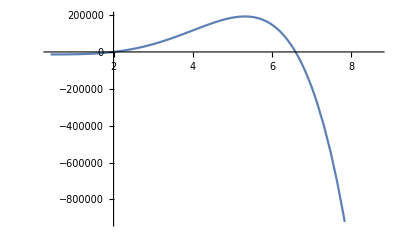

```mathematica
Plot[α[v],{v,Subscript[v, 0],Subscript[v, LSO]}]
```